```mathematica
littlewood[n_Integer,x_:x]:=1+Tuples[{1,-1},n]. x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

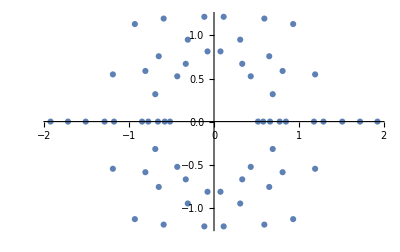

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
showRoots[n_]:=With[{s=Which[n<8,Medium,n<14,Small,True,Tiny],
r=Thread@ParallelMap[NSolveValues[#==0,x]&,littlewood[n]],
o=If[n>12,{ImageSize->1500,Axes->False},{ImageSize->Large}]},
ComplexListPlot@@{r,Sequence@@o,PlotStyle->PointSize@s}];
(* use List@@Last/@NRoots if NSolveValues is not supported *)
```

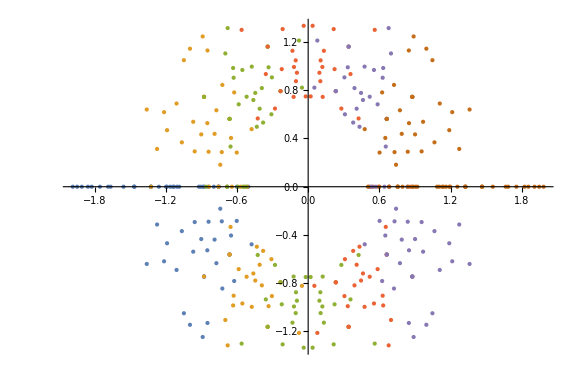

```mathematica
LaunchKernels[];
showRoots[6]
CloseKernels[];
```

```mathematica
fastShowRoots[n_]:=With[{
poly=1+Tuples[{1,-1},n]. #^Range[n]&,
root=If[n>3,Thread,Identity]@If[n>6,ParallelMap,Map]@##&,
s=AbsolutePointSize@If[n>14,1/(n-13),15-n],
l=Style[Row@{"n = ",n},FontSize->40],c=2^{1,.5}+.05},
If[n>6 && $KernelCount==0,LaunchKernels[]];
With[{p={x}~Module~root[x/.NSolve[#==0,x]&,poly@x]},
ComplexListPlot@@{p,ImageSize->1500,PlotStyle->s,PlotLabel->l,
PlotRange->{-#,#}&/@c,AspectRatio->Tr@Ratios@c,Axes->n<6}]
](* use NSolveValues instead of x/.NSolve on ver 12.3 *)
```

```mathematica
Do[Export[ToString@n<>".png",fastShowRoots@n],{n,2,15}];
```

```mathematica
Block[{t=Array[Graphics[]&,15]},
Do[t[[i-1]]=fastShowRoots[i],{i,2,Length[t]+1}];
Export["littlewood.gif",t,"DisplayDurations"->1]];
```

```mathematica
RGBColor@@@Tuples[{1,1/2,0},3]
```

{RGBColor[1, 1, 1],RGBColor[1, 1, Rational[1, 2]],RGBColor[1, 1, 0],RGBColor[1, Rational[1, 2], 1],RGBColor[1, Rational[1, 2], Rational[1, 2]],RGBColor[1, Rational[1, 2], 0],RGBColor[1, 0, 1],RGBColor[1, 0, Rational[1, 2]],RGBColor[1, 0, 0],RGBColor[Rational[1, 2], 1, 1],RGBColor[Rational[1, 2], 1, Rational[1, 2]],RGBColor[Rational[1, 2], 1, 0],RGBColor[Rational[1, 2], Rational[1, 2], 1],RGBColor[Rational[1, 2], Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, 1],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], 0, 0],RGBColor[0, 1, 1],RGBColor[0, 1, Rational[1, 2]],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], 1],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, Rational[1, 2], 0],RGBColor[0, 0, 1],RGBColor[0, 0, Rational[1, 2]],RGBColor[0, 0, 0]}